## Introduction

The “EGGS” package basically contains everything needed to simulate EGGS stuff.

This package does quantum using matrix mechanics. Operators are represented by matrices and states are represented by vectors. We generate our state space by taking the outer product of all the independent bases, so only one vector is needed to hold all the states, and all the operators have the same dimensions.

An unreasonable amount of time has been wasted trying to make everything as fast as can be: nearly everything is done (close to) instantaneously, with the exception of the Schrodinger Solver and (only for very large state spaces, >10,000) the GetPoints function, and even those have been sped up significantly. This is done by basically not using Mathematica as it’s meant to be used - all evaluation is left as late as possible to allow us to do so numerically, as opposed to using symbols. None of the functions or operators are designed to handle symbols; use symbols at your own risk.

Additionally, none of the packaged functions use parallelization . This is to allow the user to choose when/which functions to parallelize, since Mathematica only allows us to parallelize once .

Without any off-resonant terms, a regular, full, MS gate should take less than 5 seconds to solve. Including off-resonant terms within a few orders of magnitude of the dominant behavior adds roughly a factor of 10 to the computation time. For example, if we included the counter-rotating terms at twice the qubit transition (4 - 5 orders of magnitude about the detuning) as well as the carrier (3 - 4 orders of magnitude above the terms rotating at twice the qubit transition), NDSolve would take ~100 x as long. Also, note that including off- resonant terms will also eat up memory like no tomorrow, and if very, very off-resonant, can eat up all the RAM and cause a crash .

The package mainly consists of 5 parts:
1) The data generator: this basically takes trap and ion parameters and returns normal mode data as well as matches them to the operators/states.
For example, once the secular frequency has been specified through the trap parameters, ThermalState will use it to generate a Boltzmann distribution.
2) Quantum operators: the user-specified configuration is automatically reflected in these. These are held in arrays corresponding to the number of qubits and modes specified.
3) Hamiltonians: these generate Hamiltonians from the specified configuration and from user arguments.
4) the Schrodinger Solver: this basically numerically solves the interaction picture Schrodinger equation between two given points in time for the specified Hamiltonian.
5) data processing functions: these convert the wavefunctions from the Schrodinger solver into recognizable results, such as qubit state populations or average phonon numbers in each mode.

## Setup

When the package is loaded, a dialog box will open, prompting the user to enter their desired values (please make sure they are all numeric).

```mathematica
<<EGGS`
```

## Sample Case 1: Applying a Dipole Hamiltonian

This part looks a lot longer than it is, mostly because I’ve gone into a fair amount of detail on each part. Subsequent sample cases will better demonstrate how quickly we can start running gates.
In this example, we will be applying a simple dipole Hamiltonian (i.e. single-qubit gate) to both ions.

## Set Variables

Quick heads up: we’re not actually “setting” variables here (as in evaluating these variables won’t have any effect), but just storing them for clarity later on.
Each Hamiltonian requires a gate voltage, a frequency, and the ion to be operated on. Quadrupole Hamiltonians additionally require an offset (this can be zero) and a direction (i.e. radial or axial) to be specified.

```mathematica
Vm1=6;(*set gate voltage to 6V*)
δ1=0;(*on resonance with transition*)
dir1=1;(*target radial direction; 1 is radial, 2 is axial*)
```

## Get Hamiltonian

### Getting the Hamiltonian

The basic Hamiltonians involved in constructing an MS gate are included, as well as certain Hamiltonians which make life easier, such as the Hamiltonian for an MS gate itself.
If the desired Hamiltonian is not included, users can use the operators to create the desired Hamiltonian.

In this example, we want to apply dipole Hamiltonians to both ions.

```mathematica
Ham1=Sum[HE1Ex[Vm1,Δ[[ion]]+δ1,ion],{ion,2}];
```

For large splittings, the off-resonant terms add a lot of computational overhead. In these cases, what we can do is apply the Rotating Wave Approximation. A function which does this is provided:

```mathematica
Ham1RWA=Sum[HE1R1[Vm1,δ1,ion],{ion,2}];
```

Notice that the RWA’d Hamiltonian is only being driven at δ1 instead of Δ+δ1. This is because the first RWA (indicated by the “R1” in “HE1R1”) drops terms ~2Δ.
This also means that we do not need to transform RWA’d Hamiltonians, since this has already been accounted for before dropping the ~2Δ terms.

### Transforming into the Interaction Picture

We still need to transform our exact dipole Hamiltonian into the interaction picture with respect to the molecule. Um holds the time evolution operators with respect to the molecular splitting.

```mathematica
(*get time evolution operator for molecule for all ions*)
Uint1=Dot[Um[[1]],Um[[2]]];
```

```mathematica
(*take hamiltonian into interaction picture*)
Hint1=ToIntPic[Ham1,Uint1];
```

## Solve Schrodinger Equation

### Generating States

While users can simply create vectors with their desired populations, the use of outer products to define the basis makes it makes it tricky to tell which element of the basis corresponds to which state. To simplify this, the function PureState returns a vector with population of 1 in the desired state. Thermal states and Coherent states can also be created using ThermalState and CoherentState, respectively.
Also, while the function name PureState sort of implies support for mixed states, I only named it that because I couldn’t think of a better name for a regular, normal state; there is no support for mixed states.

```mathematica
(*we want to initialize our ions in the ground state: both ions are in gg, and have no phonon population*)
(*the first value argument specifies the qubit state, while the second specifies the phonon number in each mode*)
initstate1=PureState[{0,0},{0,0}];
```

```mathematica
(*alternatively, we could call GroundState, which returns the motional ground state in the specified qubit state*)
initstate1=GroundState[{0,0}];
```

```mathematica
(*set parameters for solving the schrodinger equation*)
tmin1=0;tmax1=5*^-8;
```

### Solving the Schrodinger Equation

SolveSchrodinger takes in a Hamiltonian matrix and solves the Time-Dependent interaction picture Schrodinger equation. SolveSchrodinger requires all input to be numeric (i.e. no symbols) with the except of “t”, which is treated as the independent variable for NDSolve. SolveSchrodinger returns a dispatch table, which is basically a bunch of replacement rules in a black box to make replacement go faster. This means that if you want to look at the constituent solutions (e.g. the result for ψ1[t]), you need to apply the dispatch table to the individual function, or to ψBasis, which holds the symbols for all the wavefunctions.

```mathematica
(*solve!*)
res1=SolveSchrodinger[Hint1,initstate1,tmin1,tmax1];
res1RWA=SolveSchrodinger[Ham1RWA,initstate1,tmin1,tmax1];
```

```mathematica
(*works!*)
resWavefunctions=ψBasis[[1]]/.res1
```

InterpolatingFunction[…][t]

```mathematica
(*doesn't work*)
res1[[1]]
```

Part::partd: Part specification … is longer than depth of object.

Dispatch[<484>]⟦1⟧

## Plot

### Getting Populations and Plotting

Since it can be bothersome and computationally cumbersome to correctly group the wavefunctions in our basis to yield information such as populations or phonon numbers, in-house functions have been written to quickly do this.
For example, GetPops returns the populations of each qubit state.

```mathematica
(*GetPops converts the wavefunctions into populations for each qubit state*)
resPops1=GetPops[res1];
resPops1RWA=GetPops[res1RWA];
```

```mathematica
(*plot!*)
{Plot[resPops1,{t,tmin1,tmax1},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large],Plot[resPops1RWA,{t,tmin1,tmax1},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large]}
```

{-Graphics-,-Graphics-}

From these plots, we can see that the RWA is somewhat invalid here due to the low-lying splitting of 90x2π MHz.

### Using GetPoints and ListPlot

While we can simply use Plot when we have nice behavior, doing so for fast-oscillating results will take forever. To get around this, we can instead use GetPoints to quickly get a number of points and use ListPlot.

```mathematica
(*get points*)
numPoints1=300;
resPopsPoints1=GetPoints[resPops1,tmin1,tmax1,numPoints1];
resPopsPoints1RWA=GetPoints[resPops1RWA,tmin1,tmax1,numPoints1];
```

```mathematica
(*use listplot*)
{ListPlot[Transpose[resPopsPoints1],DataRange->{tmin1,tmax1},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large],ListPlot[Transpose[resPopsPoints1RWA],DataRange->{tmin1,tmax1},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large]}
```

{-Graphics-,-Graphics-}

## Sample Case 2: Applying a Quadrupole Hamiltonian

Now that we’ve started walking, we can begin a light jog.
In this example, we are applying a single red-detuned quadrupole Hamiltonian to both ions.

## Set Variables

In this example, let’s pretend we’re using applying a single red sideband quadrupole Hamiltonian.
Again, we set our desired variables:

```mathematica
xeq2=0;(*no offset for the ion*)
Vm2=6;(*set gate voltage to 6V*)
δ2=-(wmvals[[1,1]]+3*^4);(*detuned to the first motional sideband plus some additional value*)
dir2=1;(*target radial direction; 1 is radial, 2 is axial*)
```

## Get Hamiltonians

### Getting the Hamiltonian

In the EGGS package, unlike the Barium package, Hamiltonians are provided in full, rather than being broken down into constituent parts. Additionally, Hamiltonians are automatically applied to all modes in the system. If a Hamiltonian should only be applied to a single mode, this can be done with HE2ExM1.

So to apply a sideband pulse, all we need to do is set the correct detuning and apply it to all ions:

```mathematica
Ham2=Sum[HE2Ex[xeq2,Vm2,Δ[[1]]-δ2,ion,dir2],{ion,{1,2}}];
```

As in the previous example, Hamiltonians with the RWA can also be used to reduce computational overhead.

```mathematica
Ham2RWA=Sum[HE2R1[xeq2,Vm2,-δ2,ion,dir2],{ion,{1,2}}];
```

### Transforming into the Interaction Picture

This time, we need to consider the trap Hamiltonian in addition to the molecular Hamiltonian. The time evolution operator with respect to the trap is given by Ut, where the first index indicates the direction, and the second index indicates the mode.

```mathematica
Umolint2=Dot[Um[[1]],Um[[2]]];
Utrapint2=Dot[Ut[[dir2,1]],Ut[[dir2,2]]];
```

Taking the exact Hamiltonian into the interaction picture with respect to the trap and the molecular splitting:

```mathematica
Hint2=ToIntPic[Ham2,Umolint2.Utrapint2];
```

As before, we do not have to take the RWA Hamiltonian with respect to the molecular splitting, since that has been accounted for in applying the RWA. We do, however, have to take it to the interaction picture with respect to the trap:

```mathematica
Hint2RWA=ToIntPic[Ham2RWA,Utrapint2];
```

## Solve Schrodinger Equation and Plot

### Solving

```mathematica
(*we don't choose the ground state here since we need some phonons for our sideband hamiltonians to act on*)
initstate2=PureState[{0,0},{2,2}];
(*choose our calculation time*)
tmin2=0;tmax2=250*^-6;
```

```mathematica
(*solve and get pops*)
res2=SolveSchrodinger[Hint2,initstate2,tmin2,tmax2];
res2RWA=SolveSchrodinger[Hint2RWA,initstate2,tmin2,tmax2];
```

```mathematica
resPops2=GetPops[res2];
resPops2RWA=GetPops[res2RWA];
```

We are also interested in the average phonon numbers. This can be given by GetPhonons, which gives the number of phonons in the specified mode.
Specifically, we want to know the number of phonons in the radial CoM mode (mode 1) over time.

```mathematica
resPhonons2=GetPhonons[res2,1,dir2];
resPhonons2RWA=GetPhonons[res2RWA,1,dir2];
```

### Plotting

```mathematica
(*plot qubit states*)
{Plot[resPops2,{t,tmin2,tmax2},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large],Plot[resPops2RWA,{t,tmin2,tmax2},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large]}
```

{-Graphics-,-Graphics-}

From these plots, we can see that the RWA is an acceptable approximation here.

### Phonon Numbers

Our result for average phonon number shows some oscillatory behavior. This is because the max phonon number is too low; once the phonons hit the top, they start coming back down again, yielding this behavior.
The simple solution is just to increase the max phonon number, though be careful that you don’t go too high: 10 phonons in 2 modes for 2 qubits only requires 400 states, but the same for 20 phonons requires 1600.

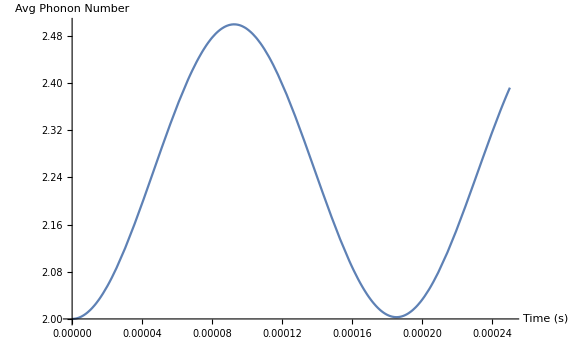
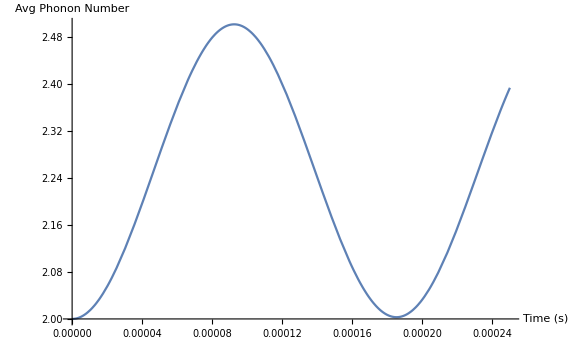

```mathematica
(*plot average phonon number*)
{Plot[resPhonons2,{t,tmin2,tmax2},AxesLabel->{"Time (s)","Avg Phonon Number"},ImageSize->Large],Plot[resPhonons2RWA,{t,tmin2,tmax2},AxesLabel->{"Time (s)","Avg Phonon Number"},ImageSize->Large]}
```

## Sample Case 3: Doing an MS Gate

Let’s upgrade to a speedy jog, just below a sprint.
In this example, we do an MS gate on two ions.

## Set Variables

```mathematica
xeq3=0;(*no offset for the ion*)
Vm3=6;(*set gate voltage to 6V*)
δ3=wmvals[[1,1]];(*detuned to the first motional sideband*)
dir3=1;(*target radial direction; 1 is radial, 2 is axial*)
```

To get the ideal detuning (as specified by the MS paper), we can call δIdeal, which gives the ideal detuning for the specified ions, using the specified mode, and as a function of gate voltage.

```mathematica
δ3Ideal=δIdeal[Vm3,{1,2},1,dir3];
```

## Get Hamiltonian

### Getting the Hamiltonian

To do an MS gate, we need to apply two pulses, each symmetrically detuned from a motional sideband (which we choose to be the radial CoM sideband).

```mathematica
Hlower3=Sum[HE2Ex[xeq3,Vm3,Δ[[1]]-(δ3+δ3Ideal),ion,dir3],{ion,{1,2}}];
Hupper3=Sum[HE2Ex[xeq3,Vm3,Δ[[1]]+(δ3+δ3Ideal),ion,dir3],{ion,{1,2}}];
```

With the RWA:

```mathematica
Hlower3RWA=Sum[HE2R1[xeq3,Vm3,-(δ3+δ3Ideal),ion,dir3],{ion,{1,2}}];
Hupper3RWA=Sum[HE2R1[xeq3,Vm3,(δ3+δ3Ideal),ion,dir3],{ion,{1,2}}];
```

Taking the Hamiltonians into the correct interaction pictures:

```mathematica
Umolint3=Dot[Um[[1]],Um[[2]]];
Utrapint3=Dot[Ut[[dir3,1]],Ut[[dir3,2]]];
```

```mathematica
Hint3=ToIntPic[Hlower3+Hupper3,Umolint3.Utrapint3];
```

```mathematica
Hint3RWA=ToIntPic[Hlower3RWA+Hupper3RWA,Utrapint3];
```

### Including the Trap

An important consideration for EGGS is the effect of the trap RF. The trap RF Hamiltonian is given by HE2Trap, and needs to be applied to every ion:

```mathematica
HamTrap=Sum[HE2Trap[xeq3,ion,dir3],{ion,{1,2}}];
```

The trap RF still needs to be taken into the interaction picture:

```mathematica
HamTrapInt=ToIntPic[HamTrap,Umolint3.Utrapint3];
```

## Solve Schrodinger Equation and Plot

### Solving

```mathematica
(*we choose the ground state for a classic MS gate*)
initstate3=PureState[{0,0},{0,0}];
```

Similar to how we got the ideal detuning, we can get the ideal gate time using τIdeal:

```mathematica
tmin3=0;tmax3=2*τIdeal[Vm3,{1,2},1,dir3];(*twice the ideal gate time just to be safe*)
```

```mathematica
(*solve*)
AbsoluteTiming[res3=SolveSchrodinger[Hint3+HamTrapInt,initstate3,tmin3,tmax3];]
AbsoluteTiming[res3RWA=SolveSchrodinger[Hint3RWA+HamTrapInt,initstate3,tmin3,tmax3];]
```

{89.304,Null}

{94.778,Null}

Compared to solving for just the RWA Hamiltonian:

```mathematica
AbsoluteTiming[SolveSchrodinger[Hint3RWA,initstate3,tmin3,tmax3];]
```

{2.00848,Null}

As we can see, including the counter-rotating terms adds significant overhead.
However, once terms oscillating at a certain frequency have been introduced, additional terms oscillating at those frequencies do not significantly change the computation time.

```mathematica
(*get pops*)
resPops3=GetPops[res3];
resPops3RWA=GetPops[res3RWA];
```

### Plotting

```mathematica
numPoints3=300;
resPopsPoints3=GetPoints[resPops3,tmin3,tmax3,300];
resPopsPoints3RWA=GetPoints[resPops3RWA,tmin3,tmax3,300];
```

Since we might get very oscillatory behavior, we first use GetPoints and ListPlot to check that nothing strange is going on:

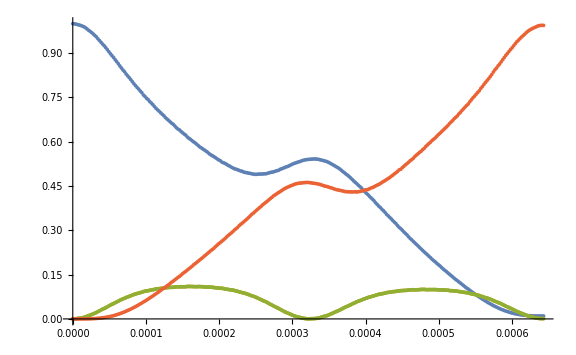
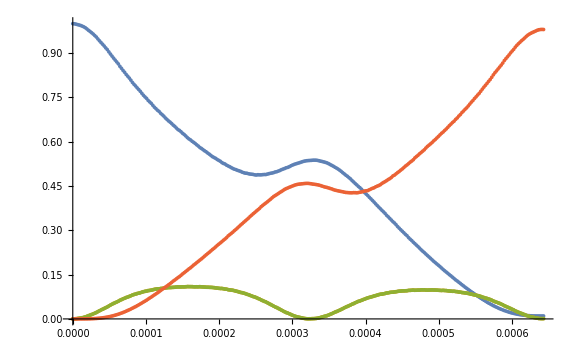

```mathematica
{ListPlot[resPopsPoints3//Transpose,ImageSize->Large,DataRange->{tmin3,tmax3}],ListPlot[resPopsPoints3RWA//Transpose,ImageSize->Large,DataRange->{tmin3,tmax3}]}
```

Since the result is well-behaved, we can use Plot to make sure we’re not missing anything:

```mathematica
{Plot[resPops3,{t,tmin3,tmax3},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large],Plot[resPops3RWA,{t,tmin3,tmax3},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large]}
```

{-Graphics-,-Graphics-}

### Fidelity

With MS gates, the result we are most interested in is the fidelity; specifically, the Bell State fidelity. To get the fidelity, we can use GetFidelity, which requires users to specify the desired qubit state (for us, that would be a Bell State).

```mathematica
bellState3=1/(√2){1,0,0,ⅈ};(*this is gg + i * ee*)
```

```mathematica
resFid3=GetFidelity[res3,bellState3];
resFid3RWA=GetFidelity[res3RWA,bellState3];
```

We want to plot the fidelity over time:

```mathematica
resFidPoints3=GetPoints[resFid3,tmin3,tmax3,numPoints3];
resFidPoints3RWA=GetPoints[resFid3RWA,tmin3,tmax3,numPoints3];
```

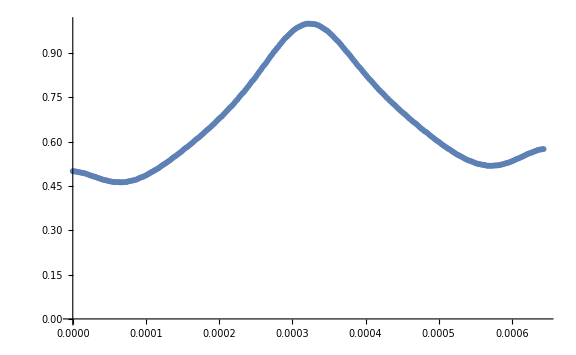
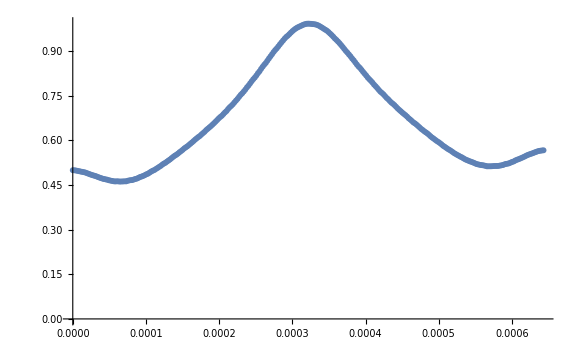

```mathematica
{ListPlot[resFidPoints3//Transpose,ImageSize->Large,DataRange->{tmin3,tmax3}],ListPlot[resFidPoints3RWA//Transpose,ImageSize->Large,DataRange->{tmin3,tmax3}]}
```

The maximum fidelities are (for the exact Hamiltonian and the RWA, respectively):

```mathematica
{Max[resFidPoints3],Max[resFidPoints3RWA]}
```

{0.999745,0.992732}

It should be noted that these fidelities may not be correct - when the gate pulses are shut off, there is still some residual oscillation. To account for this, we need to do a pulse sweep (see Example 5).

## Sample Case 4: Heating Ions for Readout

Let’s maintain the pace.
In this example, we’ll apply a heating interaction to do readout of an ion’s state.

## Set Variables

Since we’re looking to heat ions, we need to have a high phonon number. To minimize the number of states we need, we use only one mode for this example, but set the phonon ceiling to 200. This can only be done through ChangeAll[]:

```mathematica
ChangeAll[]
```

```mathematica
xeq4=0;(*no offset for the ion*)
Vm4=6;(*set gate voltage to 6V*)
δ4=wmvals[[1,1]];(*detuned to the first motional sideband*)
dir4=1;(*target radial direction; 1 is radial, 2 is axial*)
```

## Get Hamiltonian

To heat the ions, we need to apply two pulses, each symmetrically detuned from a motional sideband (which we choose to be the radial CoM sideband) plus some detuning (which we choose to be the ideal detuning). Out of convenience, from here on out, we use the Hamiltonian with the RWA applied:

```mathematica
Hlower4=Sum[HE2R1[xeq4,Vm4,-δ4,ion,dir4],{ion,{1,2}}];
Hupper4=Sum[HE2R1[xeq4,Vm4,δ4,ion,dir4],{ion,{1,2}}];
```

Taking the Hamiltonian into the interaction picture:

```mathematica
Utrapint4=Ut[[dir4,1]];
```

There is only one trap time-evolution operator in Utrapint4 since we have reduced our system to have only one mode.

```mathematica
Hint4=ToIntPic[Hlower4+Hupper4,Utrapint4];
```

## Solve Schrodinger Equation and Plot

### Solving

Again, since we only have one mode, the second argument for PureState has only one dimension:

```mathematica
initstate4=PureState[{0,0},{0}];
```

```mathematica
tmin4=0;tmax4=200*^-6;
```

```mathematica
(*solve*)
AbsoluteTiming[res4=SolveSchrodinger[Hint4,initstate4,tmin4,tmax4];]
```

{0.827665,Null}

Here, we are interested in the behavior of the populations and the average phonon numbers for each mode:

```mathematica
(*get pops*)
resPops4=GetPops[res4];
resPhonon4=GetPhonons[res4,1(*the CoM mode*),dir4];
```

### Plotting

```mathematica
numPoints4=300;
resPopsPoints4=GetPoints[resPops4,tmin4,tmax4,numPoints4];
resPhononPoints4=GetPoints[resPhonon4,tmin4,tmax4,numPoints4];
```

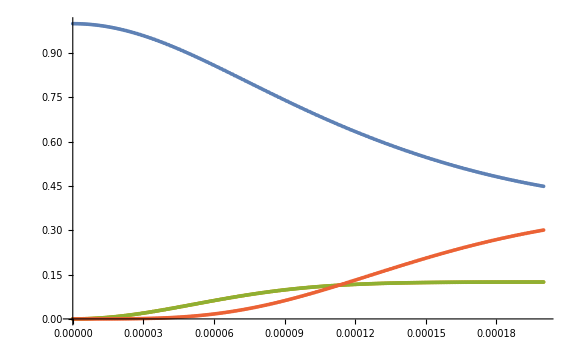

```mathematica
ListPlot[resPopsPoints4//Transpose,ImageSize->Large,DataRange->{tmin4,tmax4}]
```

We end up in an eigenstate of the Pauli-x operator, which agrees with eq (4) in EGGS v2.

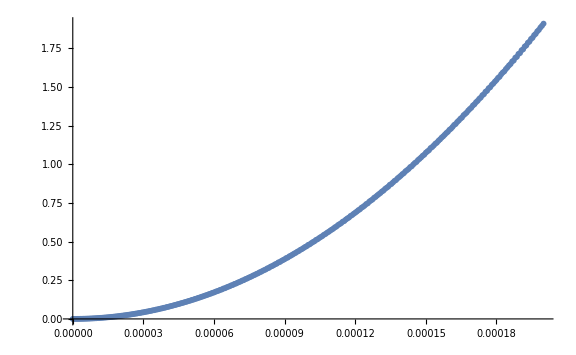

```mathematica
ListPlot[resPhononPoints4//Transpose,ImageSize->Large,DataRange->{tmin4,tmax4}]
```

This is also what we expect: heating of the mode is exponential due to the harmonic oscillator displacement operator.

## Sample Case 5: Pulse Sweeping

Time to do this properly: we want to do a pulse-shaped MS gate while accounting for the residual oscillation after the pulse is turned off.
To do this, we basically have to apply the same gate a bunch of times with different pulse-widths.

## Set Variables & Get Hamiltonian

This part is basically the same as that in Example 3.

### Variables

Variables for the gate:

```mathematica
xeq5=0;(*no offset for the ion*)
Vm5=6;(*set gate voltage to 6V*)
δ5=wmvals[[1,1]];(*detuned to the first motional sideband*)
dir5=1;(*target radial direction; 1 is radial, 2 is axial*)
δ5Ideal=δIdeal[Vm5,{1,2},1,dir5]; (*get ideal detuning*)
```

And variables for the Schrodinger solver:

```mathematica
initstate5=PureState[{0,0},{0,0}];
```

```mathematica
tmin5=0;tmax5=2*τIdeal[Vm5,{1,2},1,dir5];
```

### Getting Hamiltonians

Setting the red and blue-sideband pulses (with the RWA applied):

```mathematica
Hlower5RWA=Sum[HE2R1[xeq5,Vm5,-(δ5+δ5Ideal),ion,dir5],{ion,{1,2}}];
Hupper5RWA=Sum[HE2R1[xeq5,Vm5,(δ5+δ5Ideal),ion,dir5],{ion,{1,2}}];
```

Taking the Hamiltonians into the correct interaction pictures:

```mathematica
Umolint5=Dot[Um[[1]],Um[[2]]];
Utrapint5=Dot[Ut[[dir5,1]],Ut[[dir5,2]]];
```

```mathematica
Hint5RWA=ToIntPic[Hlower5RWA+Hupper5RWA,Utrapint5];
```

Out of interest of time, we are not going to include the trap Hamiltonian in this exercise, though this can easily be done (see Example 3).

## Pulse-Shaping

Speeding up pulse-sweeping is perhaps my biggest accomplishment so far - instead of running exponentially with the number of pulses, our implementation runs in linear time - less than twice however long it takes to run a single pulse.
We do this using two tricks:
a) instead of evaluating the pulses for the same amount of time for each pulse, we only calculate each pulse to some constant time after it finishes.
b) instead of calculating each pulse from its beginning to end, we first calculate the longest pulse. Instead of having to evaluate each pulse from the beginning, we can now evaluate each pulse starting from some constant time before the pulse at hand and the longest pulse diverge.

### Preparing the pulse shapes

For this example, our pulse-shape is based off an error function. “tl” determines the length of the pulse, and “tk” is the time constant, which determines rise/fall time.

```mathematica
pulseshape[t_,tl_,tk_]:=(Erfc[(t-tl)/(0.5*tk)])/2*(1-Erf[-t/(0.5*tk)+2 ])/2;
```

We want a time-constant of 1μs:

```mathematica
tconst=1*^-6;
```

Assume whatever device we use for pulse-shaping has a resolution of 2.5μs, and use this to create the timings for our different pulses:

```mathematica
tsweepstep=10*^-6;
tsweepmin=tsweepstep;tsweepmax=tmax5;
```

```mathematica
tsweepArr=Range[tsweepmin,tsweepmax,tsweepstep];
```

Now, to speed things up, we implement part b): we calculate the shorter pulses using the longest pulse.
The shorter pulses start to diverge from the longest pulse about 1.5x the time constant before the end of the pulse, and continue to oscillate after the pulse is finished by the same amount of time.

```mathematica
tminArr=tsweepArr-1.5*tconst;tmaxArr=tsweepArr+1.5*tconst;
```

We need to make sure that we aren’t evaluating before a pulse begins:

```mathematica
tminArr=Clip[tminArr,{0,tsweepmax}];
```

Just to check how many pulses we have to evaluate:

```mathematica
numPulses5=Length[tsweepArr]
```

64

### Creating the pulse shapes

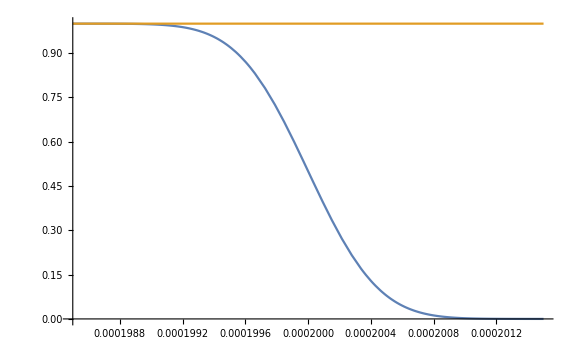

```mathematica
pulseArr=pulseshape[t,#,tconst]&/@tsweepArr;
Plot[Evaluate[{pulseArr[[{#1,#2}]]}],{t,tminArr[[#1]],tmaxArr[[#1]]},PlotRange->Full,ImageSize->Large]&[20,-1]
```

## Solve Schrodinger Equation

Let’s see how long it takes us to solve if we have to calculate each pulse in its entirety, from beginning to end:

```mathematica
AbsoluteTiming[res5All=ParallelMap[SolveSchrodinger[Hint5RWA*pulseArr[[#]],initstate5,tmin5,tmaxArr[[#]]]&,Range[numPulses5]];]
```

{152.373,Null}

Now using our speedup trick instead:

```mathematica
AbsoluteTiming[res5Fast=SolveSchrodinger[Hint5RWA*pulseArr[[-1]],initstate5,tmin5,tmaxArr[[-1]]];
res5FastPrev=((ψBasis/.res5Fast)/.#)&/@Thread[t->tminArr];
res5FastAllPoints=ParallelMap[SolveSchrodinger[Hint5RWA*pulseArr[[#]],res5FastPrev[[#]],tminArr[[#]],tmaxArr[[#]]]&,Range[numPulses5]];]
```

{48.7474,Null}

Since we’ve already applied the part a) speedup (i.e. evaluating only until a constant time after the pulse ends), we don’t exactly get an exponential speedup, but this is still sizable.

## Plotting

### Plotting Pulse Sweep

Since GetPops requires the input to be a list of replacement rules, we have to first apply GetPops to each solution in res5All:

```mathematica
resPops5=Map[GetPops,res5All];
```

We can then take the final value for each pulse:

```mathematica
resPopsPoints5=resPops5[[#]]/.{t->tmaxArr[[#]]}&/@Range[numPulses5]//Transpose;
```

Plotting:

```mathematica
ListPlot[resPopsPoints5,ImageSize->Large,DataRange->{tmin5,tmax5},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"}]
```

-Graphics-

Compared to the regular population for the longest pulse, the pulse-sweep shows little difference. Pulse-sweeping is usually more important when turning-off the pulse changes the behavior significantly, such as when the offset is sizable.

```mathematica
resPopsPointsFull5=GetPoints[resPops5[[-1]],tmin5,tmaxArr[[-1]],300]//Transpose;
```

```mathematica
ListPlot[resPopsPointsFull5,PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large]
```

-Graphics-

### Plotting Fidelity

As before, we use the following Bell State:

```mathematica
bellState5=1/(√2){1,0,0,ⅈ};(*this is gg + i * ee*)
```

Again, we have to first apply GetFidelity before taking the values:

```mathematica
resFid5=Map[GetFidelity[#,bellState5]&,res5All];
```

```mathematica
resFidPoints5=resFid5[[#]]/.{t->tmaxArr[[#]]}&/@Range[numPulses5];
```

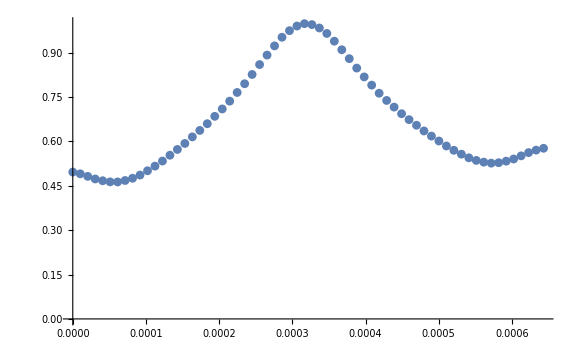

```mathematica
ListPlot[resFidPoints5,ImageSize->Large,DataRange->{tmin5,tmax5}]
```

The maximum fidelity is:

```mathematica
Max[resFidPoints5]
```

0.998066